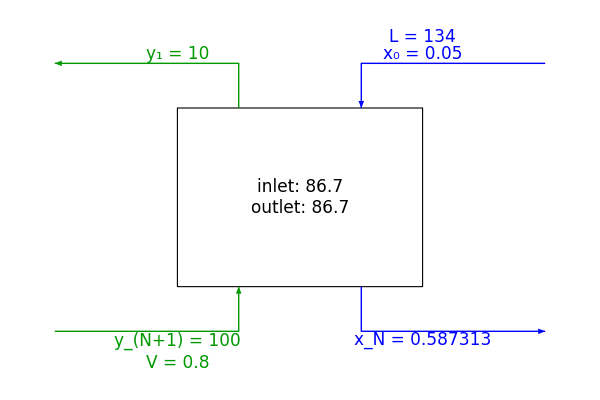

```mathematica
Module[{L,V,x0,y1,yn1,yop,xN,colL,colV,w,h},
L=134;V=0.8;
x0=0.05;y1=10;yn1=100;

yop[x_]:=L/V*(x-x0)+y1;
xN=x/.Solve[yop[x]==yn1,x][[1]];

colL=Blue;colV=RGBColor[0,0.6,0];
w=5;h=10;

Graphics[{Thick,Arrowheads@0.1,
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{w,h}]},
{colL,Arrow[{{1.5*w,1.25*h},{0.75*w,1.25*h},{0.75*w,h}}],Arrow[{{0.75*w,0},{0.75*w,-0.25*h},{1.5*w,-0.25*h}}]},
{colV,Arrow[{{0.25*w,h},{0.25*w,1.25*h},{-0.5*w,1.25*h}}],Arrow[{{-0.5*w,-0.25*h},{0.25*w,-0.25*h},{0.25*w,0}}]},

Text[Style[Row@{Subscript[Style["x",Italic],0]," = ",x0},17,colL],{w,1.25*h},{0,-1.2}],
Text[Style[Row@{Style[Subscript["x","N"],Italic]," = ",xN},17,colL],{w,-0.25*h},{0,1.5}],
Text[Style[Row@{Style["L",Italic]," = ",L},17,colL],{w,1.4*h}],

Text[Style[Row@{Subscript[Style["y",Italic],1]," = ",y1},17,colV],{0,1.25*h},{0,-1.2}],
Text[Style[Row@{Subscript[Style["y",Italic],Row@{Style["N",Italic],"+1"}]," = ",yn1},17,colV],{0,-0.25*h},{0,1.5}],
Text[Style[Row@{Style["V",Italic]," = ",V},17,colV],{0,-0.43*h}],

Text[Style[Column[{
Row@{"inlet: ",x0*L+yn1*V},
Row@{"outlet: ",xN*L+y1*V}
}],17],{0.5*w,0.5*h}]
},ImageSize->{600,400}]
]
```